```mathematica
alphabet = {"а","б","в","г","д","е","ё","ж","з","и","й","к","л","м","н","о","п","р","с","т","у","ф","х","ц","ч","ш","щ","ъ","ы","ь","э","ю","я", " ", "\n", "\t","a","b","c","d","e","f","g","h","i","j","q","k","l","m","o","p","q","r","s","t","u","v","w","x","y","z"};
text = Import["C:\\Users\\User\\Desktop\\pg10.txt"];
data= StringSplit[StringDelete[ToLowerCase[text], Except[alphabet]]];
```

```mathematica
Commonest[data, 100]
```

{the,of,kig,this,is,for,at,o,ad,with,you,may,it,give,or,was,by,i,god,upo,said,let,there,be,that,from,day,he,were,a,made,which,so,uto,oe,lad,after,his,to,them,also,set,hath,every,their,sayig,us,make,ma,our,have,all,ow,him,behold,shall,had,because,these,are,whe,they,lord,before,ot,but,wet,up,ito,out,thou,shalt,will,take,her,my,therefore,ye,we,your,as,thy,thee,hast,me,go,childre,eve,came,if,agaist,come,sos,do,house,thigs,dow,people,saith,israel}

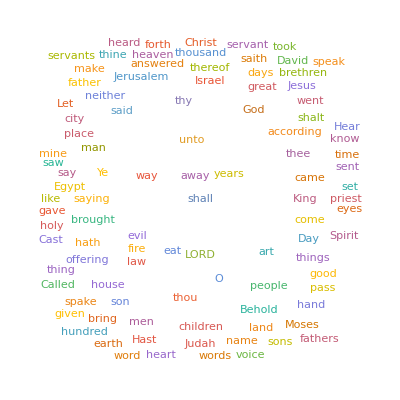

```mathematica
WordCloud[text]
```